# Solving 3 equations(R, d, y)

```mathematica
Clear[r]
d[t_]:=Sqrt[r^2+R[t]^2-2*r(r*Cos[ϕ[t]]^2-Sin[ϕ[t]]*Sqrt[R[t]^2-r^2*Cos[ϕ[t]]^2])];
FullSimplify[D[d[t],t]]
```

((√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]]) (R[t] R'[t]+r Cos[ϕ[t]] (√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]]) ϕ'[t]))/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2) √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))

```mathematica
Clear[r,k]
Eb[t_]:=k*π*(1-Sqrt[1-(r*Cos[ϕ[t]]/R[t])^2]);
FullSimplify[D[Eb[t], t]]
```

-(k π r^2 Cos[ϕ[t]] (Cos[ϕ[t]] R'[t]+R[t] Sin[ϕ[t]] ϕ'[t]))/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)

```mathematica
Clear[r,k,σ]
Es[t_]:=4*π*σ*R[t]^2*(1-Sqrt[1-(r*Cos[ϕ[t]]/R[t])^2]);
FullSimplify[D[Es[t], t]]
```

1/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t])4 π σ ((r^2 Cos[ϕ[t]]^2+2 (-1+√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^2) R'[t]-r^2 Cos[ϕ[t]] R[t] Sin[ϕ[t]] ϕ'[t])

```mathematica
V[t_]:=π/(12*d[t])*(R[t]-d[t]+r)^2*(d[t]^2+2*d[t]*r-3*r^2+2*d[t]*R[t]+6*r*R[t]-3*R[t]^2);
FullSimplify[D[V[t], t]]
```

(π (r+d[t]-R[t]) (r-d[t]+R[t]) ((r-d[t]-R[t]) (r+d[t]+R[t]) d'[t]+4 d[t] R[t] R'[t]))/(4 d[t]^2)

```mathematica
expr=(1/(4 d[t]^2))π (r+d[t]-R[t]) (r-d[t]+R[t]) ((r-d[t]-R[t]) (r+d[t]+R[t]) Derivative[1][d][t]+4 d[t] R[t] Derivative[1][R][t]);
sol=Solve[expr==α,Derivative[1][d][t]];
FullSimplify[sol]
```

{{d'[t]→(4 d[t] (α d[t]+π R[t] (-r-d[t]+R[t]) (r-d[t]+R[t]) R'[t]))/(π (r-d[t]-R[t]) (r+d[t]-R[t]) (r-d[t]+R[t]) (r+d[t]+R[t]))}}

```mathematica
expr1=((Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2]+r Sin[ϕ[t]]) (R[t] Derivative[1][R][t]+r Cos[ϕ[t]] (Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2]+r Sin[ϕ[t]]) Derivative[1][ϕ][t]))/(Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sqrt[R[t]^2+r (-r Cos[2 ϕ[t]]+2 Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sin[ϕ[t]])]);
expr2=(4 d[t] (α d[t]+π R[t] (-r-d[t]+R[t]) (r-d[t]+R[t]) Derivative[1][R][t]))/(π (r-d[t]-R[t]) (r+d[t]-R[t]) (r-d[t]+R[t]) (r+d[t]+R[t]));


collected=FullSimplify[expr1-expr2];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Dcoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Ecoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Fterm=-collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Dcoeff*Derivative[1][R][t]+Ecoeff*Derivative[1][ϕ][t]==Fterm;
```

R[t] (-((4 d[t])/((-r+d[t]+R[t]) (r+d[t]+R[t])))+(√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]])/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2) √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]]))))

(r Cos[ϕ[t]] √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2))

(4 α d[t]^2)/(π (d[t]^4+(r^2-R[t]^2)^2-2 d[t]^2 (r^2+R[t]^2)))

```mathematica
EL[t_]:=2*π*r*Γ Cos[ϕ[t]];
FullSimplify[D[EL[t], t]]
```

-2 π r Γ Sin[ϕ[t]] ϕ'[t]

```mathematica
Clear[k,r,σ,X,z,y,w,v,Np,Γ, P]
expr3=-((k*Pi*r^2*Cos[ϕ[t]]*
    (Cos[ϕ[t]]*Derivative[1][R][
       t] + R[t]*Sin[ϕ[t]]*
      Derivative[1][ϕ][t]))/
   (Sqrt[1 - (r^2*Cos[ϕ[t]]^2)/
       R[t]^2]*R[t]^3));
expr4=(1/(Sqrt[1 - (r^2*Cos[ϕ[t]]^2)/
       R[t]^2]*R[t]))*
  (4*Pi*σ*((r^2*Cos[ϕ[t]]^2 + 
      2*(-1 + Sqrt[1 - 
          (r^2*Cos[ϕ[t]]^2)/
           R[t]^2])*R[t]^2)*
     Derivative[1][R][t] - 
    r^2*Cos[ϕ[t]]*R[t]*Sin[ϕ[t]]*
     Derivative[1][ϕ][t]));
expr5=2*π*r*(-Γ)*Sin[ϕ[t]]*Derivative[1][ϕ][t];
expr6=α*P;
expr7=(G/π)*z^2*w*v*Cos[ϕ[t]]*Np/y;
expr8=X;
lhs=expr7+expr8;
rhs=expr3+expr4+expr5+expr6;

collected=FullSimplify[lhs-rhs];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Acoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Bcoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Cterm=-collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Acoeff*Derivative[1][R][t]+Bcoeff*Derivative[1][ϕ][t]==Cterm;
```

(π (k r^2 Cos[ϕ[t]]^2-4 r^2 σ Cos[ϕ[t]]^2 R[t]^2-8 σ (-1+√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^4))/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)

(π r (k r Cos[ϕ[t]]+(4 r σ Cos[ϕ[t]]+2 Γ √(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^2) Sin[ϕ[t]])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^2)

-X+P α-(G Np v w z^2 Cos[ϕ[t]])/(π y)

# Initial

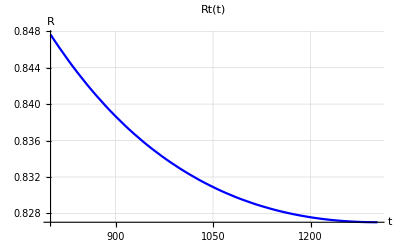

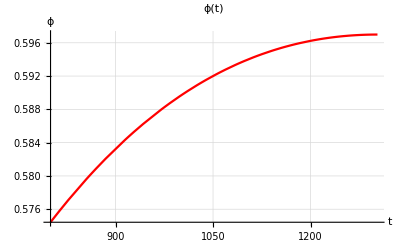

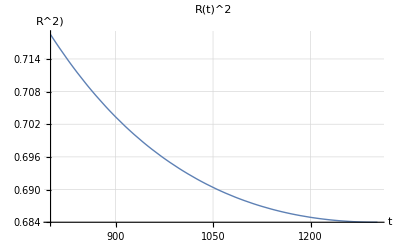

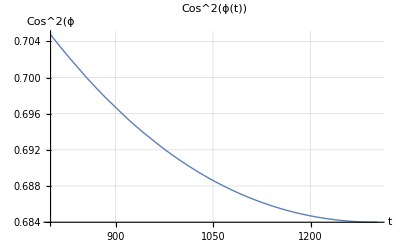

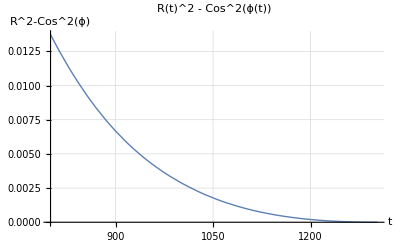

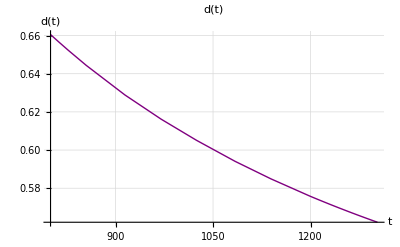

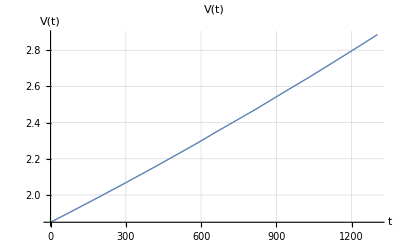

0.827032+0. ⅈ

0.596989+0. ⅈ

0.562524+0. ⅈ

4.66385×10^6+0. ⅈ

838554.+0. ⅈ

-0.981481

2239.7+0. ⅈ

1261.01+0. ⅈ

-0.000121192+0. ⅈ

```mathematica
ClearAll["Global`*"]

(*Constants*)

(*w=30*10^-9;
z=3.4*10^-9;
y=2*10^-9;
σ=4.5*10^-3;*)
r=1;
(*v=15*10^-9;
k=11250*10^-21;
α=0.058*10^-18/3600;*)
αt=(1/60)/11250;
αp=(1/(60*64));
P=80*10^3;
(*Np=2;*)

Gt=1;(*Value of G*)
Xt=0.1;(*External Energy*)
Γt=0;(*value of Line tension*)
σt=800; (*value of surface term*)
Rt0=4;
ph0=0.3;
tmin=0;
tmax=3600;
tminp=800;
finalTime=1300;
(*Define d,A-F as functions of R[t],ph[t]*)
dt[t_]:=Sqrt[1+Rt[t]^2-2*(Cos[ϕ[t]]^2-Sin[ϕ[t]]*Sqrt[Rt[t]^2-Cos[ϕ[t]]^2])];

A1[t_]:=(π (Cos[ϕ[t]]^2-Rt[t]^2σt Cos[ϕ[t]]^2-2 σt Rt[t]^4 (-1+Sqrt[1-(Cos[ϕ[t]]^2)/Rt[t]^2])))/( Sqrt[1-(Cos[ϕ[t]]^2)/Rt[t]^2] Rt[t]^3);

B1[t_]:= (π Cos[ϕ[t]]+(σt Cos[ϕ[t]]+2 Γt Sqrt[1-(Cos[ϕ[t]]^2)/Rt[t]^2]) Rt[t]^2) Sin[ϕ[t]]/(Sqrt[1-(Cos[ϕ[t]]^2)/Rt[t]^2] Rt[t]^2);

C1[t_]:=-Xt+P αt-Gt Cos[ϕ[t]];

D1[t_]:=Rt[t] (-((4 dt[t])/((-1+dt[t]+Rt[t]) (1+dt[t]+Rt[t])))+(Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2]+Sin[ϕ[t]])/(Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2] Sqrt[(Rt[t]^2+(- Cos[2 ϕ[t]]+2 Sqrt[(-Cos[ϕ[t]]^2+Rt[t]^2)] Sin[ϕ[t]]))]));

E1[t_]:=(Cos[ϕ[t]] Sqrt[Rt[t]^2+ (- Cos[2 ϕ[t]]+2 Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2] Sin[ϕ[t]])])/Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2];

F1[t_]:=(4 αp dt[t]^2)/(π r^2 (dt[t]^4+(1-Rt[t]^2)^2-2 dt[t]^2 (1+Rt[t]^2)));

(*Checking*)
(*params={Rt[t]->4,ϕ[t]->0.3};
Evaluate/@{dt[t], A1[t],B1[t], C1[t], D1[t], E1[t], F1[t]}/.params*)
(****************)

(*RHS of system*)
Rdot[t_]:=(E1[t]*C1[t]-B1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);
phdot[t_]:=(-D1[t]*C1[t]+A1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);

(*Define ODEs*)
eqns={Rt'[t]==Rdot[t],ϕ'[t]==phdot[t],Rt[0]==Rt0,ϕ[0]==ph0};

(*Numerical solution*)sol=NDSolve[eqns,{Rt,ϕ},{t,tmin,tmax},Method->{"StiffnessSwitching"}, MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];

V[t_]:=π/(12*dt[t])*(Rt[t]-dt[t]+1)^2*(dt[t]^2+2*dt[t]*1-3+2*dt[t]*Rt[t]+6*Rt[t]-3*Rt[t]^2)

(*Plot R vs t*)
rPlot=Plot[Evaluate[Rt[t]/.sol],{t,tminp,tmax},PlotLabel->"Rt(t)",AxesLabel->{"t","R"},PlotStyle->Blue,PlotRange->All,GridLines->Automatic]

(*Plot φ vs t*)
phPlot=Plot[Evaluate[ϕ[t]/.sol],{t,tminp,tmax},PlotLabel->"ϕ(t)",AxesLabel->{"t","ϕ"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]

test1Plot=Plot[Evaluate[Rt[t]^2/.sol],{t,tminp,tmax},PlotLabel->"R(t)^2",AxesLabel->{"t","R^2)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
test2Plot=Plot[Evaluate[Cos[ϕ[t]]^2/.sol],{t,tminp,tmax},PlotLabel->" Cos^2(ϕ(t))",AxesLabel->{"t"," Cos^2(ϕ"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
testPlot=Plot[Evaluate[Rt[t]^2-Cos[ϕ[t]]^2/.sol],{t,tminp,tmax},PlotLabel->"R(t)^2 - Cos^2(ϕ(t))",AxesLabel->{"t","R^2-Cos^2(ϕ)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
dtPlot=Plot[Evaluate[dt[t]/.sol],{t,tminp, tmax},PlotLabel->"d(t)",AxesLabel->{"t","d(t)"},PlotStyle->{Thick,Purple},GridLines->Automatic,PlotRange->All]
testVPlot=Plot[Evaluate[V[t]^2/.sol],{t,0,tmax},PlotLabel->" V(t)",AxesLabel->{"t"," V(t)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
(*Display both plots*)
GraphicsGrid[{{rPlot},{phPlot}, {testPlot}, {test1Plot}, {test2Plot}, {dtPlot}}];

RtFinal=Rt[finalTime]/.sol//First//N
phiFinal=ϕ[finalTime]/.sol//First//N
dtFinal=dt[finalTime]/.sol//First//N
A1Final=A1[finalTime]/.sol//First//N
B1Final=B1[finalTime]/.sol//First//N
C1Final=C1[finalTime]/.sol//First//N
D1Final=D1[finalTime]/.sol//First//N
E1Final=E1[finalTime]/.sol//First//N
F1Final=F1[finalTime]/.sol//First//N
```

```mathematica
Clear[R,r,ψ]
exp=Sqrt[R^2+r^2-2 R r Cos[ψ]];
sol=Solve[exp==r,R];
FullSimplify[sol]
```

{{R→0},{R→2 r Cos[ψ]}}

```mathematica
ClearAll["Global`*"]
d[t_]:=Sqrt[r^2+R[t]^2-2*r(r*Cos[ϕ[t]]^2+Sin[ϕ[t]]*Sqrt[R[t]^2-r^2*Cos[ϕ[t]]^2])];
FullSimplify[D[d[t],t]]
```

-((√(-r^2 Cos[ϕ[t]]^2+R[t]^2)-r Sin[ϕ[t]]) (-R[t] R'[t]+r Cos[ϕ[t]] (√(-r^2 Cos[ϕ[t]]^2+R[t]^2)-r Sin[ϕ[t]]) ϕ'[t]))/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2) √(R[t]^2-r (r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))

```mathematica
ClearAll["Global`*"]
V[t_]:=π/(12*d[t])*(R[t]-d[t]+r)^2*(d[t]^2+2*d[t]*r-3*r^2+2*d[t]*R[t]+6*r*R[t]-3*R[t]^2);
FullSimplify[D[V[t],t]]
```

(π (r+d[t]-R[t]) (r-d[t]+R[t]) ((r-d[t]-R[t]) (r+d[t]+R[t]) d'[t]+4 d[t] R[t] R'[t]))/(4 d[t]^2)

```mathematica
ClearAll["Global`*"]
expr=(1/(4 d[t]^2))π (r+d[t]-R[t]) (r-d[t]+R[t]) ((r-d[t]-R[t]) (r+d[t]+R[t]) Derivative[1][d][t]+4 d[t] R[t] Derivative[1][R][t]);
sol=Solve[expr==α,Derivative[1][d][t]];
FullSimplify[sol]
```

{{d'[t]→(4 d[t] (α d[t]+π R[t] (-r-d[t]+R[t]) (r-d[t]+R[t]) R'[t]))/(π (r-d[t]-R[t]) (r+d[t]-R[t]) (r-d[t]+R[t]) (r+d[t]+R[t]))}}

```mathematica
Clear[r,k]
Eb[t_]:=k*π*(1+Sqrt[1-(r*Cos[ϕ[t]]/R[t])^2]);
FullSimplify[D[Eb[t], t]]
```

(k π r^2 Cos[ϕ[t]] (Cos[ϕ[t]] R'[t]+R[t] Sin[ϕ[t]] ϕ'[t]))/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)

```mathematica
Clear[r,k,σ]
Es[t_]:=4*π*σ*R[t]^2*(1+Sqrt[1-(r*Cos[ϕ[t]]/R[t])^2]);
FullSimplify[D[Es[t], t]]
```

(4 π σ ((-r^2 Cos[ϕ[t]]^2+2 (1+√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^2) R'[t]+r^2 Cos[ϕ[t]] R[t] Sin[ϕ[t]] ϕ'[t]))/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t])

```mathematica
Clear[k,r,σ,X,z,y,w,v,Np,Γ, P]
expr3=(k π r^2 Cos[ϕ[t]] (Cos[ϕ[t]] Derivative[1][R][t]+R[t] Sin[ϕ[t]] Derivative[1][ϕ][t]))/(Sqrt[1-(r^2 Cos[ϕ[t]]^2)/R[t]^2] R[t]^3);
expr4=(4 π σ ((-r^2 Cos[ϕ[t]]^2+2 (1+Sqrt[1-(r^2 Cos[ϕ[t]]^2)/R[t]^2]) R[t]^2) Derivative[1][R][t]+r^2 Cos[ϕ[t]] R[t] Sin[ϕ[t]] Derivative[1][ϕ][t]))/(Sqrt[1-(r^2 Cos[ϕ[t]]^2)/R[t]^2] R[t]);
expr5=2*π*r*(-Γ)*Sin[ϕ[t]]*Derivative[1][ϕ][t];
expr6=α*P;
expr7=(G/π)*z^2*w*v*Cos[ϕ[t]]*Np/y;
expr8=X;
lhs=expr7+expr8;
rhs=expr3+expr4+expr5+expr6;

collected=FullSimplify[lhs-rhs];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Acoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Bcoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Cterm=-collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Acoeff*Derivative[1][R][t]+Bcoeff*Derivative[1][ϕ][t]==Cterm;
```

(π (-k r^2 Cos[ϕ[t]]^2+4 r^2 σ Cos[ϕ[t]]^2 R[t]^2-8 σ (1+√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^4))/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)

-(π r (k r Cos[ϕ[t]]+(4 r σ Cos[ϕ[t]]-2 Γ √(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^2) Sin[ϕ[t]])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^2)

-X+P α-(G Np v w z^2 Cos[ϕ[t]])/(π y)

```mathematica
ClearAll["Global`*"]
```

```mathematica
expr1=((Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2]-r Sin[ϕ[t]]) (-R[t] Derivative[1][R][t]+r Cos[ϕ[t]] (Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2]-r Sin[ϕ[t]]) Derivative[1][ϕ][t]))/(Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sqrt[R[t]^2-r (r Cos[2 ϕ[t]]+2 Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sin[ϕ[t]])]);
expr2=(4 d[t] (α d[t]+π R[t] (-r-d[t]+R[t]) (r-d[t]+R[t]) Derivative[1][R][t]))/(π (r-d[t]-R[t]) (r+d[t]-R[t]) (r-d[t]+R[t]) (r+d[t]+R[t]));


collected=FullSimplify[expr1-expr2];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Dcoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Ecoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Fterm=-collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Dcoeff*Derivative[1][R][t]+Ecoeff*Derivative[1][ϕ][t]==Fterm;
```

-(4 d[t] R[t])/((-r+d[t]+R[t]) (r+d[t]+R[t]))+(R[t] (-√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]]))/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2) √(R[t]^2-r (r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))

(r Cos[ϕ[t]] √(R[t]^2-r (r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2))

(4 α d[t]^2)/(π (d[t]^4+(r^2-R[t]^2)^2-2 d[t]^2 (r^2+R[t]^2)))

# Final

```mathematica
ClearAll["Global`*"]

(*Constants*)

(*w=30*10^-9;
z=3.4*10^-9;
y=2*10^-9;
σ=4.5*10^-3;*)
r=1;
(*v=15*10^-9;
k=11250*10^-21;
α=0.058*10^-18/3600;*)
αt=(1/60)/11250;
αp=(1/(60*64));
P=80*10^3;
(*Np=2;*)

Gt=1;(*Value of G*)
Xt=-.1;(*External Energy*)
Γt=1;(*value of Line tension*)
σt=800; (*value of surface term*)
Rt0=0.825;
ph0=0.60;

tmin=0;
tmax=2000;
tminp=0;
finalTime=2000;
(*Define d,A-F as functions of R[t],ph[t]*)
dt[t_]:=Sqrt[1+Rt[t]^2-2*(Cos[ϕ[t]]^2+Sin[ϕ[t]]*Sqrt[Rt[t]^2-Cos[ϕ[t]]^2])];

A1[t_]:=((-π Cos[ϕ[t]]^2+σt Cos[ϕ[t]]^2 Rt[t]^2-2 σ (1+Sqrt[1-( Cos[ϕ[t]]^2)/Rt[t]^2]) Rt[t]^4))/(Sqrt[1-( Cos[ϕ[t]]^2)/Rt[t]^2] R[t]^3);

B1[t_]:= -(( (π Cos[ϕ[t]]+( σt Cos[ϕ[t]]-2 Γt Sqrt[1-( Cos[ϕ[t]]^2)/Rt[t]^2]) Rt[t]^2) Sin[ϕ[t]])/(Sqrt[1-( Cos[ϕ[t]]^2)/Rt[t]^2] Rt[t]^2));

C1[t_]:=-Xt+P αt-Gt Cos[ϕ[t]];

D1[t_]:=-((4 dt[t] Rt[t])/((-1+dt[t]+Rt[t]) (1+dt[t]+Rt[t])))+(Rt[t] (-Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2]+Sin[ϕ[t]]))/(Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2] Sqrt[Rt[t]^2-r (Cos[2 ϕ[t]]+2 Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2] Sin[ϕ[t]])]);

E1[t_]:=( Cos[ϕ[t]] Sqrt[Rt[t]^2- ( Cos[2 ϕ[t]]+2 Sqrt[- Cos[ϕ[t]]^2+Rt[t]^2] Sin[ϕ[t]])])/Sqrt[- Cos[ϕ[t]]^2+Rt[t]^2];

F1[t_]:=(4 αp dt[t]^2)/(π (dt[t]^4+(1-Rt[t]^2)^2-2 dt[t]^2 (1+Rt[t]^2)));

(*Checking*)
(*params={Rt[t]->4,ϕ[t]->0.3};
Evaluate/@{dt[t], A1[t],B1[t], C1[t], D1[t], E1[t], F1[t]}/.params*)
(****************)

(*RHS of system*)
Rdot[t_]:=(E1[t]*C1[t]-B1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);
phdot[t_]:=(-D1[t]*C1[t]+A1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);

(*Define ODEs*)
eqns={Rt'[t]==Rdot[t],ϕ'[t]==phdot[t],Rt[0]==Rt0,ϕ[0]==ph0};

(*Numerical solution*)sol=NDSolve[eqns,{Rt,ϕ},{t,tmin,tmax},Method->{"StiffnessSwitching"}, MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];


(*Plot R vs t*)
rPlot=Plot[Evaluate[Rt[t]/.sol],{t,tminp,tmax},PlotLabel->"Rt(t)",AxesLabel->{"t","R"},PlotStyle->Blue,PlotRange->All,GridLines->Automatic]

(*Plot φ vs t*)
phPlot=Plot[Evaluate[ϕ[t]/.sol],{t,tminp,tmax},PlotLabel->"ϕ(t)",AxesLabel->{"t","ϕ"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]

test1Plot=Plot[Evaluate[Rt[t]^2/.sol],{t,tminp,tmax},PlotLabel->"R(t)^2",AxesLabel->{"t","R^2)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
test2Plot=Plot[Evaluate[Cos[ϕ[t]]^2/.sol],{t,tminp,tmax},PlotLabel->" Cos^2(ϕ(t))",AxesLabel->{"t"," Cos^2(ϕ"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
testPlot=Plot[Evaluate[Rt[t]^2-Cos[ϕ[t]]^2/.sol],{t,tminp,tmax},PlotLabel->"R(t)^2 - Cos^2(ϕ(t))",AxesLabel->{"t","R^2-Cos^2(ϕ)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
dtPlot=Plot[Evaluate[dt[t]/.sol],{t,tminp, tmax},PlotLabel->"d(t)",AxesLabel->{"t","d(t)"},PlotStyle->{Thick,Purple},GridLines->Automatic,PlotRange->All]
(*Display both plots*)
GraphicsGrid[{{rPlot},{phPlot}, {testPlot}, {test1Plot}, {test2Plot}, {dtPlot}}];

RtFinal=Rt[finalTime]/.sol//First//N
phiFinal=ϕ[finalTime]/.sol//First//N
dtFinal=dt[finalTime]/.sol//First//N
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

0.823129+3.36385×10^-10 ⅈ

0.6029-4.77799×10^-10 ⅈ

0.567033-0.0305116 ⅈ